LevelScheme examples: Data plots

M. A. Caprio, Department of Physics, University of Notre Dame

## Package initialization

If you have not already loaded the LevelScheme package since starting this Mathematica session, you must do so now.  See the user guide for information first on installing the package and then on loading it at the beginning of each Mathematica session.

```mathematica
Get["LevelScheme`"];
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.51 (February 23, 2011)
View color paletteVisit home page  -Graphics-

## Disclaimer

Data plotting: These examples involves the LevelScheme data plotting functions, which are not yet documented and still under development.

## Simple multipanel data plot (with data styles and legend) -- Nuclear mass predictions

Experimental data -- entered here as a list

```mathematica
ExptData={{0, 0., None}, {1, -7.363, 7.363}, {2, -19.843, 12.480}, {3, -27.776, 7.933}, {4, -38.906, 11.13}, {5, -46.321, 7.415}, {6, -56.715, 10.394}, {7, -63.991, 7.276}, {8, -73.936, 9.945}};
%//TableForm
```

0 | 0. | None
1 | -7.363 | 7.363
2 | -19.843 | 12.48
3 | -27.776 | 7.933
4 | -38.906 | 11.13
5 | -46.321 | 7.415
6 | -56.715 | 10.394
7 | -63.991 | 7.276
8 | -73.936 | 9.945

Theory data -- here we define a formula to calculate the data points

```mathematica
EGSSeniority[G_,Omega_,N_?EvenQ]=-1/4*G*N*(2*Omega-N+2);
EGSSeniority[G_,Omega_,N_?OddQ]=-1/4*G*(N-1)*(2*Omega-N+1);
SeniorityData[epsilon_,G_]:=Table[
{N,
N*epsilon+EGSSeniority[G,4,N],
If[N>0,
-(epsilon+EGSSeniority[G,4,N]-EGSSeniority[G,4,N-1]),
None
]
},
{N,0,8}
];
```

And let us store the results...

```mathematica
TheoryData=SeniorityData[-9.323,0.75];
%//TableForm
```

0 | 0. | None
1 | -9.323 | 9.323
2 | -21.646 | 12.323
3 | -30.219 | 8.573
4 | -41.792 | 11.573
5 | -49.615 | 7.823
6 | -60.438 | 10.823
7 | -67.511 | 7.073
8 | -77.584 | 10.073

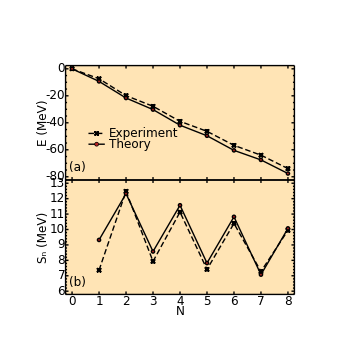

```mathematica
Figure[
{

Multipanel[
{2,1},
XPlotRanges->{0,8},
YPlotRanges->{{-80,0},{6,13}},
Margin->40,
XFrameTicks->LinTicks[0,8,1,1],
ExtendRange->0.03,
XFrameLabels->"N",BufferB->3.5,
YFrameLabels->{"E (MeV)","S_n (MeV)"},BufferL->4.5,
PanelLetterCorner->{-1,-1},
Background->Moccasin
],

(* define common data styles in advance, to be used systematically across the plots *)
SetOptions[DataSymbol,SymbolSize->4],
DefineDataStyle["expt",DataLine->{Dashing->True},DataSymbol->{SymbolShape->"Cross",Thickness->1.5}],
DefineDataStyle["theory",DataSymbol->{FillColor->Firebrick}],

(* panel 1 *)
FigurePanel[{1,1}],
DataPlot[ExptData,DataStyle->"expt"],
DataPlot[TheoryData,DataStyle->"theory"],

(* legend in panel 1 *)
DataLegend[{0.1,0.45},
{
{"expt","Experiment"},
{"theory","Theory"}
}
],

(* panel 2  *)
FigurePanel[{2,1}],
DataPlot[DataSet[ExptData,DataColumns->{1,3}],DataStyle->"expt"],
DataPlot[DataSet[TheoryData,DataColumns->{1,3}],DataStyle->"theory"],

},
ImageSize->72*{5,5}
]
```

## Some simple demos of data plotting options

### Error bars

Although it is anticipated that other ways of specifying error bars will be added later...

```mathematica
Data={{0.,0.},{0.39269908169872414,0.3826834323650898},{0.7853981633974483,0.7071067811865475},{ErrorValue[1.1781,0.2],ErrorValue[0.92388,{-0.4,0.2}]},{1.5707963267948966,1.},{1.9634954084936207,0.9238795325112867},{2.356194490192345,0.7071067811865475},{2.748893571891069,0.3826834323650898},{3.141592653589793,0.},{3.5342917352885173,-0.3826834323650898},{3.9269908169872414,-0.7071067811865475},{4.319689898685965,-0.9238795325112867},{4.71238898038469,-1.},{5.105088062083414,-0.9238795325112867},{5.497787143782138,-0.7071067811865475},{5.890486225480862,-0.3826834323650898},{6.283185307179586,0.}};
```

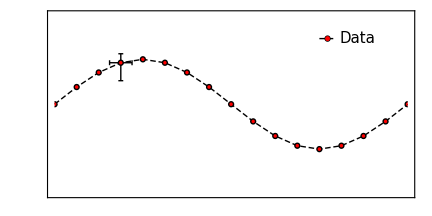

```mathematica
Figure[
{

SetOptions[DataLine,Dashing->4],
SetOptions[DataSymbol,SymbolShape->"Circle",FillColor->Red,SymbolSize->6],

DataPlot[
Data,Tag->set[1]
],

DataLegend[{0.75,0.9},{{set[1],"Data"}},Length->10,Gap->5,FontSize->15]

},
PlotRange->{{0,2*Pi},{-2,2}}, ImageSize->72*{6,3},
Frame->True
]
```

### Log-log plotting (with error bars)

```mathematica
Data={{0.,0.},{0.39269908169872414,0.3826834323650898},{0.7853981633974483,0.7071067811865475},{ErrorValue[1.1781,0.2],ErrorValue[0.92388,{-0.4,0.2}]},{1.5707963267948966,1.},{1.9634954084936207,0.9238795325112867},{2.356194490192345,0.7071067811865475},{2.748893571891069,0.3826834323650898}};
```

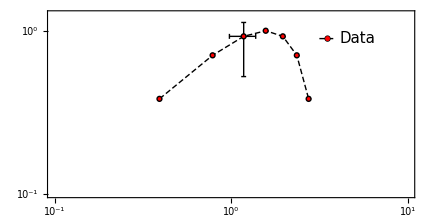

```mathematica
Figure[
{

SetOptions[DataValues,AxisScaling->{Log,Log}],
SetOptions[DataLine,Dashing->4],
SetOptions[DataSymbol,SymbolShape->"Circle",FillColor->Red,SymbolSize->6],

DataPlot[
Data,Tag->set[1]
],


DataLegend[{0.75,0.9},{{set[1],"Data"}},Length->10,Gap->5,FontSize->15]

},
PlotRange->{{-1,1},{-1,0.1}}, ImageSize->72*{6,3},
Frame->True,FrameTicks->{LogTicks[-2,2],LogTicks[-2,2],None,None}
]
```

### Step line shape

```mathematica
Data=Table[N@{x,Sin[x]},{x,0,2*Pi,Pi/8}]
```

{{0.,0.},{0.392699,0.382683},{0.785398,0.707107},{1.1781,0.92388},{1.5708,1.},{1.9635,0.92388},{2.35619,0.707107},{2.74889,0.382683},{3.14159,0.},{3.53429,-0.382683},{3.92699,-0.707107},{4.31969,-0.92388},{4.71239,-1.},{5.10509,-0.92388},{5.49779,-0.707107},{5.89049,-0.382683},{6.28319,0.}}

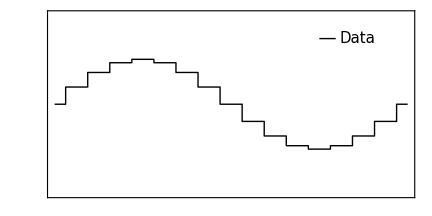

```mathematica
Figure[
{

SetOptions[DataLine,LineShape->"Step"],
SetOptions[DataSymbol,Show->False],
DataPlot[Data,Tag->set[1]],


DataLegend[{0.75,0.9},{{set[1],"Data"}},Length->10,Gap->5,FontSize->15]

},
PlotRange->{{0,2*Pi},{-2,2}}, ImageSize->72*{6,3},
Frame->True
]
```

## Plotting imported data, plus a complicated diagram -- Shell model basis dimension plot

define coordinate system for three-dimensional harmonic oscillator potential
	(the specific numbers have to do with the quantum mechanics)

```mathematica
ShellDimension[N_?NonNegative]:=(N+1)*(N+2);
HOE[N_?NonNegative]:=N+3/2;
```

```mathematica
HOScale[N1_?NonNegative]:=Module[
{yMax,xMax},
yMax=HOE[N1+1/2];
xMax=Sqrt[yMax];
{1/xMax,1/yMax}
];
```

define function to plot harmonic oscillator -- and also set the local coordinate system for dots and arrows to be plotted on top of the harmonic oscillator

```mathematica
Options[HOPlot]={HOPotlOpts->{Thickness->2},HOLevelOpts->{}};
HOPlot[N1_?NonNegative,OptionsPattern[]]:=Module[
{x,y,yMax,xMax,ScaleFunction},
{

(* set global scale -- plot up to half a level above N1 *)
yMax=HOE[N1+1/2],
xMax=Sqrt[yMax],
SetScale[{1/xMax,1/yMax}],

(* plot levels -- behind potential*)
Table[
{
y=HOE[N],
SchemeLine[{{-Sqrt[y],y},{Sqrt[y],y}},OptionValue[HOLevelOpts]]
},
{N,0,N1}
],

(* plot potential *)
SchemeLine[Plot[x^2,{x,-xMax,+xMax}],OptionValue[HOPotlOpts]],

}
];
```

define functions to draw dots

```mathematica
Options[HOPoint]={Scale->0.1};
HOPoint[N_?NonNegative,(k_Integer)?Positive,OptionsPattern[]]:=Module[
{x,y},
y=HOE[N];
x=OptionValue[Scale]*(-1/2*(ShellDimension[N]-1)+(k-1));
{x,y}
];
```

```mathematica
Options[HODot]={DotRadius->Point[2],DotOptions->{},Occupied->True};
HODot[N_?NonNegative,(k_Integer)?Positive,OptionsPattern[]]:=Module[
{x,y},
{
SchemeCircle[HOPoint[N,k],OptionValue[DotRadius],OptionValue[DotOptions],ShowFill->OptionValue[Occupied]]
}
];
```

Basis data import

```mathematica
Nuclei={"8Be","12C","16O","20Ne","24Mg"}
```

{8Be,12C,16O,20Ne,24Mg}

```mathematica
Do[
FileName="LevelScheme/ExampleData/dims_"<>x<>"_"<>DataSet<>".dat";
Print[FileName];
DimensionData[x,DataSet]=Import[FileName];
Print@DimensionData[x,DataSet],
{x,Nuclei},{DataSet,If[x=="12C",{"m","j-0"},{"m"}]}
];
```

LevelScheme/ExampleData/dims_8Be_m.dat

{{0,51},{2,5103},{4,143792},{6,2217754},{8,23346724},{10,187304858},{12,1222330036},{14,6770401490},{16,32787482114},{18,141871838200},{20,557615009428}}

LevelScheme/ExampleData/dims_12C_m.dat

{{0,51},{2,17725},{4,1118926},{6,32598920},{8,594496743},{10,7830355795},{12,80791831793},{14,687586662589},{16,5000645950810},{18,31883820915478},{20,181683757394328}}

LevelScheme/ExampleData/dims_12C_j-0.dat

{{0,9},{2,1223},{4,54692},{6,1260008},{8,19001265},{10,212516741},{12,1896492709},{14,14154420593},{16,91266485614},{18,520524613808},{20,2673031464496}}

LevelScheme/ExampleData/dims_16O_m.dat

{{0,1},{2,1245},{4,345365},{6,26483625},{8,996878170},{10,23709299558},{12,406327725468},{14,5425818528852},{16,59403380960781},{18,552459133073711},{20,4478768089572347}}

LevelScheme/ExampleData/dims_20Ne_m.dat

{{0,640},{2,542072},{4,74668421},{6,4392390341},{8,152243743459},{10,3638757261551},{12,65707716312680},{14,950734053547124},{16,11478322774747285},{18,118565877620996657},{20,913788212122942315}}

LevelScheme/ExampleData/dims_24Mg_m.dat

{{0,28503},{2,17941903},{4,2330225841},{6,142516975375},{8,5371018298923},{10,142772869772281},{12,2902084251756085},{14,47571333233735467},{16,577737308933988851},{18,3946162315235158335},{20,17360663094100388619}}

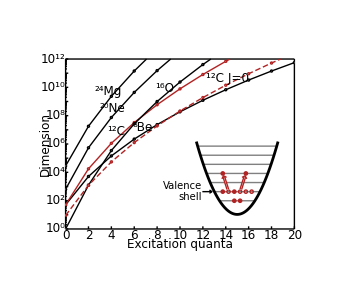

```mathematica
NucleusLabels={
"8Be"->NucleusBox["Be",NuclearA->8],
"12C"->NucleusBox["C",NuclearA->12],
"16O"->NucleusBox["O",NuclearA->16],
"20Ne"->NucleusBox["Ne",NuclearA->20],
"24Mg"->NucleusBox["Mg",NuclearA->24]
};
NucleusPosns={
"8Be"->0.40,
"12C"->0.30,
"16O"->0.53,
"20Ne"->0.29,
"24Mg"->0.27
};
NucleusColors={
"12C"->Firebrick,
_->Black
};
Figure[
{
Multipanel[
{{0,1},{0,1}},
{1,1},
ShowPanelLetter->False,
Margin->40
],

FigurePanel[
{1,1},
PlotRange->{{0,20},{0,12}},
FrameTicks->{LinTicks[0,20,2,1],LogTicks[0,20,TickLabelStep->2]},
LabB->"Excitation quanta",BufferB->3.0,
LabL->"Dimension",BufferL->4.0
],
SetOptions[DataValues,AxisScaling->{None,Log}],
SetOptions[DataSymbol,FillColor->White],
Table[
{
DataPlot[
DimensionData[x,"m"],
Tag->Curve[x,"m"],
DataLine->{Color->Replace[x,NucleusColors]},
DataSymbol->{Color->Replace[x,NucleusColors]}
],
DataLabel[Curve[x,"m"],LabT->Replace[x,NucleusLabels],PosnT->Replace[x,NucleusPosns]]
},
{x,Nuclei}
],

With[
{x="12C"},
{
SetOptions[DataLine,Color->Replace[x,NucleusColors]],
SetOptions[DataSymbol,Color->Replace[x,NucleusColors]],
DataPlot[DimensionData[x,"j-0"],DataLine->{Dashing->4},Tag->Curve[x,"j-0"]],
DataLabel[Curve[x,"j-0"],LabT->Row[{Replace[x,NucleusLabels]," ",textit["J"],"=0"}],PosnT->0.75],
}
],

ScaledFigurePanel[{{0.5,1},{0,0.60}},PlotRange->{{-1,1},{0,1}},ExtendRange->0.2,Frame->False],
HOPlot[6,HOLevelOpts->{Color->Gray}],

SetOptions[HOPoint,Scale->0.4],
SetOptions[HODot,DotOptions->{Color->Firebrick}],
Table[
{
HODot[0,k]
},
{k,1,ShellDimension[0]}
],
Table[
{
HODot[1,k,Occupied->(k≤4)&&(k≠2)&&(k≠4)],
},
{k,1,ShellDimension[1]}
],

(* excitations *)
ExcitationArrowStyle={ArrowType->MultilineArrow,Width->2,HeadLength->3,HeadLip->2,Color->Firebrick,FillColor->White,HeadRecess->3,TailRecess->3},
HODot[3,ShellDimension[3]/2-2],
SchemeArrow[{HOPoint[1,2],HOPoint[3,ShellDimension[3]/2-2]},ExcitationArrowStyle],
HODot[3,ShellDimension[3]/2+2],
SchemeArrow[{HOPoint[1,4],HOPoint[3,ShellDimension[3]/2+2]},ExcitationArrowStyle],
(*ManualLabel[HOPoint[3,ShellDimension[3]/2]+{0,0.2},"4Ω",Color->Firebrick,Background->Automatic,FontSize->13],*)

(*ManualLabel[{-Sqrt[HOE[1]],HOE[1]},StackText[Center,0,{"Valence","shell"}],CallOutVector->{+5,0}]*)

(* valence shell label *)
P0={-Sqrt[HOE[1]],HOE[1]},
SchemeArrow[P0+{-1,0},P0,LabT->StackText[Center,0,{"Valence","shell"}],OrientationT->Horizontal,OffsetT->{+0.75,0},FontSize->10,HeadLength->3,HeadLip->2,HeadRecess->3,TailRecess->3],

},
ImageSize->72*{5,4},
PlotRange->{{0,1},{0,1}}
]
```